## Schrodinger Equation

## Interpretation and Time-Dependence

This is our twenty-fourth notebook. In this notebook, we will build on the intuition for the solutions found in the previous notebook. We will interpret and “normalize” the solutions. These are known as stationary solutions. Then we will reintroduce time, see that energy closely relates to time-dependence, and finally combine solutions with different energies and different time-dependencies to get non-stationary (moving) solutions of Schrodinger’s equation.

### Exact Energy Levels

One of the things that comes out of an exact solution is the exact energy levels. They are:

E_n=ℏω(n+1/2)

First we should compare that with the values we got by fiddling with energy in the previous notebook.

```mathematica
energy[n_]:=n+1/2
```

Allowing for “experimental” error, did you get something close to 1/2, 3/2, 5/2, 7/2, and 9/2?

### Exact Solutions (Wave Functions)

The other thing that comes out of an exact solution is the exact wave functions, but rather than attempt to give you some kind of general formula for ψ_n(x) that is valid for all n, I’ll just define the first five (with n=0,1,2,3, and 4):

```mathematica
psi[x_,0]:=1/Pi^(1/4)Exp[-x^2/2];
psi[x_,1]:=1/Pi^(1/4)√2 x Exp[-x^2/2];
psi[x_,2]:=1/Pi^(1/4)1/(√2)(2 x^2-1)Exp[-x^2/2];
psi[x_,3]:=1/Pi^(1/4)1/(√3)(2 x^3-3x)Exp[-x^2/2];
psi[x_,4]:=1/Pi^(1/4)1/(√384)(16 x^4-48 x^2+12)Exp[-x^2/2];
```

Let’s plot those first five exact solutions:

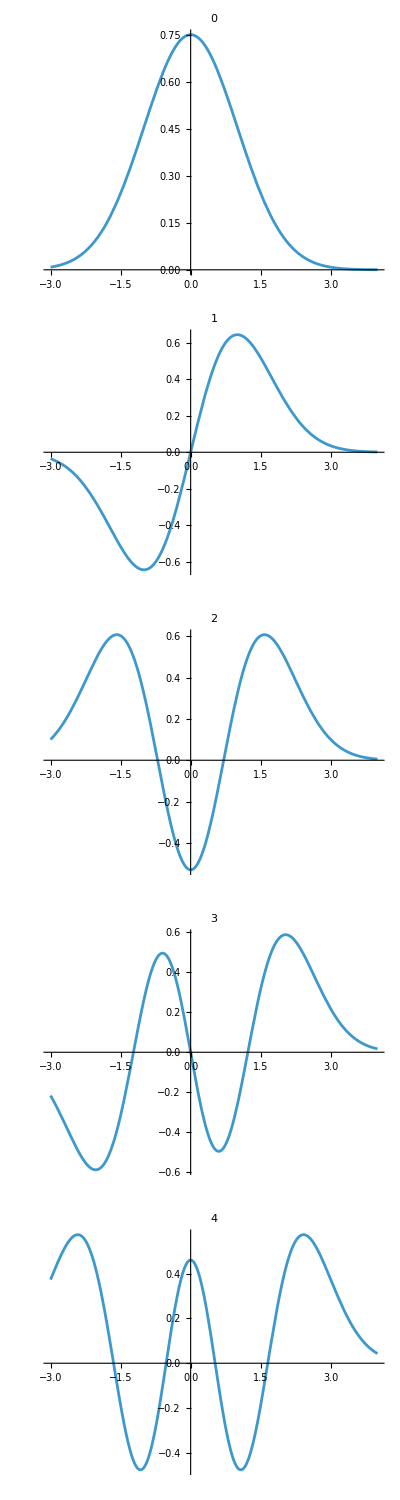

```mathematica
Table[Plot[psi[x,n],{x,-3,4},PlotLabel->n],{n,0,4}] // Column
```

Again you could compare with your sketches from the previous notebook.

### Exact Solutions — Observables

The next intellectual leap that the quantum physicists of the 1920s made is that the wave function is itself unobservable! Furthermore they allowed the value of the wave function at each point x (or at each point x at each time t) to be a complex number!! Complex numbers are numbers that can have both real and imaginary parts. It’s almost like these guys were tripping. I cannot fathom how they came up with such crazy stuff. So what is observable!?

If you square the wave function (thereby losing some information), what comes out of that operation is the thing that is observable. Let’s plot the squared wave functions:

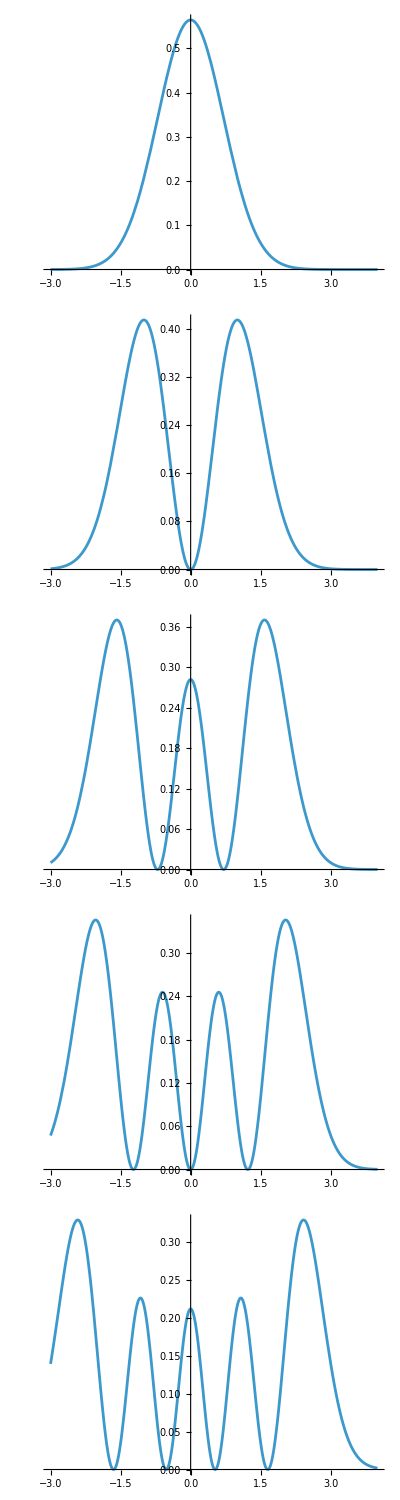

```mathematica
Table[Plot[Abs[psi[x,n]]^2,{x,-3,4}],{n,0,4}] // Column
```

### Exact Solutions — Normalization

The squared wave function, which is observable, is interpreted as the probability of finding the particle at the point in question. The “squaring” I am talking about always yields a real number. In Mathematica we use Abs[] and then square the result, because Abs[] has been arranged to do the right thing with complex numbers.

The wave functions I squared above were already real (not complex), so I could have used ordinary squaring, but let’s already start getting in the habit of using the kind of squaring you have to use when complex numbers appear.

Because the interpretation of the square of the wave function is that it is the probability for finding the particle at a position, and the probability of finding the electron somewhere must be one, then the sum of the probability of finding it any specific place must add up to 1. You can eyeball the curves above and perhaps satisfy yourself that they each have area under the curve 1, or you can make Mathematica compute the area under each of the curves:

```mathematica
Table[Integrate[Abs[psi[x,n]]^2,{x,-Infinity,Infinity}],{n,0,4}]
```

{1,1,1,1,1}

Now you finally know why ψ'(-longWays)=0.1 was arbitrary. We were just going to multiply by a constant so that the total probability came out to 1. That is precisely the reason for all the messy constants like 1/Pi^(1/4)1/(√384) that showed up out in front of the exact wave functions. These are called “normalized” wave functions.

### Quantum Superpositions (aka Mixtures)

Like waves on a guitar string, quantum mechanics allows any superposition of wave functions to be a wave function. Let’s consider an arbitrary superposition of the first five wave functions. The most general superposition, now including the time dependence looks like this:

```mathematica
timeDependentPsi[x_,t_]:=Expand[Sum[c[n]psi[x,n]Exp[-Sqrt[-1] energy[n]t],{n,0,4}]]
timeDependentProbabability[x_,t_]:=Abs[timeDependentPsi[x,t]]^2
timeDependentProbabability[x,t]//TraditionalForm
```

Abs[(√(2/3) ⅇ^(-x^2/2-(9 ⅈ t)/2) c(4) x^4)/π^(1/4)+(2 ⅇ^(-x^2/2-(7 ⅈ t)/2) c(3) x^3)/(√3 π^(1/4))+(√2 ⅇ^(-x^2/2-(5 ⅈ t)/2) c(2) x^2)/π^(1/4)-(√6 ⅇ^(-x^2/2-(9 ⅈ t)/2) c(4) x^2)/π^(1/4)+(√2 ⅇ^(-x^2/2-(3 ⅈ t)/2) c(1) x)/π^(1/4)-(√3 ⅇ^(-x^2/2-(7 ⅈ t)/2) c(3) x)/π^(1/4)+(ⅇ^(-x^2/2-(ⅈ t)/2) c(0))/π^(1/4)-(ⅇ^(-x^2/2-(5 ⅈ t)/2) c(2))/(√2 π^(1/4))+(√(3/2) ⅇ^(-x^2/2-(9 ⅈ t)/2) c(4))/(2 π^(1/4))]^2

### A Short Rant (a plug for what you have been learning)

<begin-rant>

Looking at the bit of algebra on the previous page that Mathematica did for us, I am reminded why I taught this course in Mathematica, not Python. Yes, you can make these things happen in a Jupyter notebook, but it is grossly clumsier. Python has been trying to graft symbolic manipulation into its arsenal of tools, but Mathematica is symbolic at its most basic level, and it does algebra easily and elegantly.

At some point you will probably have to learn Python to work with a team. You now know enough software development techniques that you do not need to sign up for a Python course. Instead, grab this book and teach yourself Python:

-Graphics-

It is another language, and it will take you months, just like learning Mathematica took you months, but you are now sophisticated enough that you don’t need another course.

The one area in which you have no sophistication yet is object-oriented programming. If you wanted to take another computer science course, you could take a 200-level course titled something like “Object-Oriented Programming in Java.” Java is a premier object-oriented language, but Python has also grafted objects into its ever-enlarging hodge-podge of methodologies, so it might be titled “Object-Oriented Programming in Python” and before you begin the course, they would expect you to have learned all the basics of Python.

<end-rant />

### Animating Time Dependence

So that the total probability in the superposition of finding the electron somewhere is still 1, we must have:

Abs[c[0]]^2+Abs[c[1]]^2+Abs[c[2]]^2+Abs[c[3]]^2+Abs[c[4]]^2=1

#### A Trivial Cross-Check

If we take a pure state, one that only has c[2]=1 for example, and all the rest 0, we should get back a stationary probability density function. Let’s do that case:

```mathematica
Animate[Plot[timeDependentProbabability[x,t]/.{c[0]->0,c[1]->0,c[2]->1,c[3]->0,c[4]->0},{x,-4,4},PlotRange->{All,{0,1}}],{t,0,2Pi}]
```

#### Recovering Time-Dependence

So now, as our final manipulation of the one-dimensional harmonic oscillator solutions, we will recover time-dependence by considering a superposition (a mixture) of states with different energies?

What solution of Abs[c[0]]^2+Abs[c[1]]^2+Abs[c[2]]^2+Abs[c[3]]^2+Abs[c[4]]^2=1 can you come up with that has c[2]=c[3]=c[4]=0 and c[1]=c[2]?

Copy-and-paste the essential part out of the Animate[] above,  paste it into the animate below, and make the necessary changes to the constants c[]:

```mathematica
Animate[Graphics[Disk[]],{t,0,2Pi}]
```